```mathematica
Remove["Global`*"]

funP[m_] := IntegerPartitions[m]

funI[n_, m_, p_, a_, b_] := Binomial[n + 1, Length[p]]*(a - b)^(m - Length[p])*
   Fold[Function[{c, v}, (c*(a^(v + 1) - b^(v + 1)))/(v + 1)], 1, p]*
   Factorial[m]/Fold[Function[{c, v}, c*v!], 1, p]

funM[n_,m_,a_,b_] :=Fold[Function[{s,p} ,s + funI[n,m,p,a,b]],0,funP[m]]

funImult[n_,m_,p_,a_,b_,d_] := funI[n,m,p,a,b]*((n+1-Length[p])*(a^(d+1) - b^(d+1))/(d+1)/(a-b)+ Fold[Function[{c,v},c+(v+1)*(a^(v+1+d) - b^(v+1+d))/(a^(v+1) - b^(v+1))/(v+1+d)], 0,p])

funK [n_,m_,k_,a_,b_] :=Simplify[Fold[Function[{s,p} ,s + Simplify[funImult[n,m,p,a,b,k]]],0,funP[m]]]

funF[n_,m_,k_,r_,a_,b_] := Simplify[(a+b)^r*(funK[n-2,m-k-r,k,a,b]+(a^k+b^k) *funM[n-2,m-k-r,a,b] )]

funG[n_,m_,y_,z_] :=Sum[ (-z)^k/(n+1)^(m-k)*Binomial[m,k]*Sum[Binomial[m-k,r]*funF[n,m,k,r,y - 1/2, y - z - 1/2],{r,0,m-k}],{k,0,m}]

funT[n_,k_] := Sum[1/x,{x,n, n+k}]/(k+1)

funPoly[n_,m_] := Fold[Function[{s,v}, s + Fold[Function[{ss,vv}, ss + vv],0,v]],0,MapIndexed[Function[{v,d}, v*funT[n+d[[2]]-1-m, d[[1]]-1]], CoefficientList[funG[n,m,y ,z],{y,z}],{2}]]

p = Simplify[funPoly[n,2]]
```

(96+12 n+4 n^2-15 n^3-5 n^4+3 n^5+n^6)/(12 n (1+n)^2 (4-4 n-n^2+n^3))

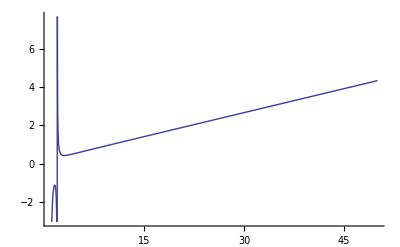

(96+12 n+4 n^2-15 n^3-5 n^4+3 n^5+n^6)/(12 n (1+n)^2 (4-4 n-n^2+n^3))[50]

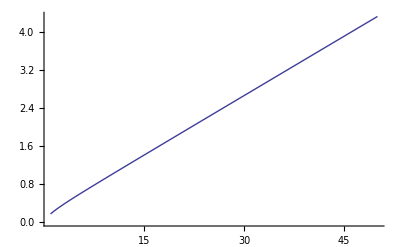

```mathematica
Plot[n*p,{n,1,50}]
Plot[n/12 + n/6/(n+1), {n,1,50}]
```

```mathematica
(* Tests *)
funI[5,2,{2},a,b] ==
```

2 (a-b) (a^3-b^3)